## Data Import

```mathematica
d = Import["Projects/Wolfram/AllCustomersSP24B.csv", "Dataset", "HeaderLines"->1]
```

```mathematica
ff = Import["Downloads/SP24FFRoster.csv", "Dataset", "HeaderLines"->1];
```

```mathematica
hustle = Import["Downloads/24SPHustleHouseLeagueRoster.csv", "Dataset", "HeaderLines"->1];
```

```mathematica
su24bballcamp = Import["Downloads/SU24BBBallCamp.csv", "Dataset", "HeaderLines"->1];
```

```mathematica
sp24HoopAcademy = Import["Downloads/SP24HoopAcademy.csv", "Dataset", "HeaderLines"->1];
```

```mathematica
sp24KIDS =  Import["Downloads/SP24KIDS1-6.csv", "Dataset", "HeaderLines"->1];
```

```mathematica
bsny24AAU =  Import["Downloads/bsny24AAU.csv", "Dataset", "HeaderLines"->1];
```

## Maps

```mathematica
locStrings = Map[StringRiffle[{#[["Address Line 1"]], #City, #[["State / Province"]]}, " "]&, bsny24AAU] ;
```

```mathematica
geoLocsSP24KIDS = FindGeoLocation/@ locStrings;
```

```mathematica
geoLocsbsny24AAU = FindGeoLocation/@ locStrings;
```

```mathematica
geoLocsHustle = FindGeoLocation/@ locStrings;
```

```mathematica
geoLocsFF = geoLocs;
```

```mathematica
geoLocsSU24Bball = geoLocs;
```

```mathematica
geoLocsSP24HoopAcademy = geoLocs;
```

```mathematica
Length[geoLocsbsny24AAU]
```

169

```mathematica
outLocs = Prepend[{QuantityMagnitude[Latitude[#]], QuantityMagnitude[Longitude[#]]}& /@ Normal[DeleteMissing[geoLocsbsny24AAU]], {"Latitude", "Longitude"}];
```

```mathematica
Export["Projects/Wolfram/Fastbreak/geoLocsBSNY24AAU.csv", outLocs];
```

```mathematica
gHustle = GeoListPlot[geoLocsHustle, GeoCenter->Entity["AdministrativeDivision",{"NewYorkCounty","NewYork","UnitedStates"}], GeoRange->Quantity[5,"Miles"]]
```

-Graphics-

```mathematica
gbsny24AAU = GeoListPlot[geoLocsbsny24AAU, GeoCenter->Entity["AdministrativeDivision",{"NewYorkCounty","NewYork","UnitedStates"}], GeoRange->Quantity[5,"Miles"]]
```

-Graphics-

```mathematica
gSP24Kids =  GeoListPlot[geoLocsSP24KIDS, GeoCenter->Entity["AdministrativeDivision",{"NewYorkCounty","NewYork","UnitedStates"}], GeoRange->Quantity[5,"Miles"]]
```

-Graphics-

```mathematica
gSU24Bball =  GeoListPlot[geoLocsSU24Bball, GeoCenter->Entity["AdministrativeDivision",{"NewYorkCounty","NewYork","UnitedStates"}], GeoRange->Quantity[5,"Miles"]]
```

-Graphics-

```mathematica
gSP24HoopAcademy =  GeoListPlot[geoLocsSP24HoopAcademy, GeoCenter->Entity["AdministrativeDivision",{"NewYorkCounty","NewYork","UnitedStates"}], GeoRange->Quantity[5,"Miles"]]
```

-Graphics-

```mathematica
gFF
```

-Graphics-

## Histograms

```mathematica
data = bsny24AAU;
name = "BSNY24AAU";
```

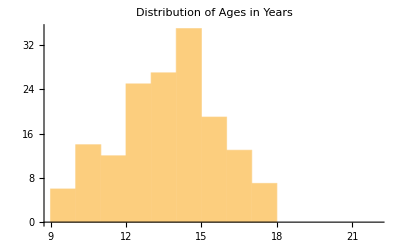

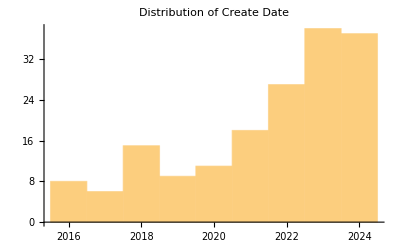

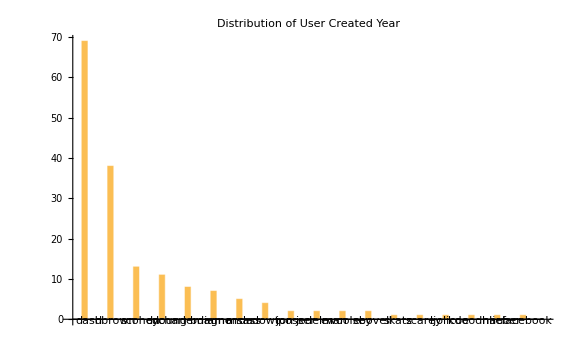

{Projects/Wolfram/Fastbreak/BSNY24AAU/data.csv,Projects/Wolfram/Fastbreak/BSNY24AAU/ages.pdf,Projects/Wolfram/Fastbreak/BSNY24AAU/createDate.pdf,Projects/Wolfram/Fastbreak/BSNY24AAU/createUser.pdf}

```mathematica
ages =Histogram[ages = DateDifference[ FromDateString[#], Today, "Years"]&/@ DeleteCases[data[All,"Birthdate"], ""], PlotLabel->"Distribution of Ages in Years"]
createDate =Histogram[createDates = DateValue[FromDateString[#], "Year"]&/@ DeleteCases[data[All,"Create Date"], ""], PlotLabel->"Distribution of Create Date"]
createUser= Tally[ToLowerCase/@data[All, "Create User"]];
 BarChart[Labeled[Reverse[#],#[[1]]]&/@Normal[ReverseSortBy[createUser, #[[2]]&]], ImageSize->Large, PlotLabel->"Distribution of User Created Year"]
MapThread[Export["Projects/Wolfram/Fastbreak/"<>name<>"/"<>#1, #2]&, {{"data.csv","ages.pdf", "createDate.pdf", "createUser.pdf"}, {data,ages, createDate, createUser}}]
```

## Single Page Output

```mathematica
programs = {"SU24UESBballcamp", "SP24KIDS", "SP24Hustle", "SP24HoopAcademy", "SP24FF", "SP24BSNYAAU"}
```

{SU24UESBballcamp,SP24KIDS,SP24Hustle,SP24HoopAcademy,SP24FF,SP24BSNYAAU}

```mathematica
Export[NotebookDirectory[]<>"order.txt", programs]
```

/Users/erichegonzales/Projects/Wolfram/Fastbreak/Program Analysis/order.txt

```mathematica
SystemOpen[DirectoryName[AbsoluteFileName["order.txt"]]]
```

```mathematica
MapThread[Import["Projects/Wolfram/Fastbreak/"<>name<>"/"<>#1, #2]&, {{"data.csv","ages.pdf", "createDate.pdf", "createUser.pdf"}, {data,ages, createDate, createUser}}]
```

```mathematica
importrepos = NotebookDirectory[]<>#<>"/"&/@ programs
```

{/Users/erichegonzales/Projects/Wolfram/Fastbreak/Program Analysis/SU24UESBballcamp/,/Users/erichegonzales/Projects/Wolfram/Fastbreak/Program Analysis/SP24KIDS/,/Users/erichegonzales/Projects/Wolfram/Fastbreak/Program Analysis/SP24Hustle/,/Users/erichegonzales/Projects/Wolfram/Fastbreak/Program Analysis/SP24HoopAcademy/,/Users/erichegonzales/Projects/Wolfram/Fastbreak/Program Analysis/SP24FF/,/Users/erichegonzales/Projects/Wolfram/Fastbreak/Program Analysis/SP24BSNYAAU/}

```mathematica
getPaths[repo_]:= repo<>#&/@ {"map.jpeg", "ages.pdf", "createDate.pdf",  "createUser.pdf"}
```

```mathematica
imgpathsList = getPaths/@ importrepos;
```

```mathematica
imgs = Flatten[Import/@ #]&/@ imgpathsList
```

{{-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-}}

```mathematica
split = Partition[imgs, 3]
```

{{{-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-}},{{-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-}}}

```mathematica
grids = Grid/@ split
```

{-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-,-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-}

```mathematica
Export[NotebookDirectory[]<>"page2.jpeg", grids[[2]]]
```

/Users/erichegonzales/Projects/Wolfram/Fastbreak/Program Analysis/page2.jpeg